# Standardized ML approach

```mathematica
SeedRandom[2017]
```

```mathematica
unifyData[yes_List,no_List]:= Join[Thread[Table[yes[[x,All,All]],{x,Length[yes]}]-> "Yes"],Thread[Table[no[[x,All,All]],{x,Length[no]}]->"No"]]
```

```mathematica
partitionTrainTest[data_List,frac_Real]:={trainDataYesAndNo = RandomSample[data,Round@(Length[data]*frac)],
testDataYesAndNo = Complement[data,trainDataYesAndNo]}
```

```mathematica
rotateLabel[label_]:=Style[Rotate[label,Pi/4],30,Bold,Opacity[0.2],FontFamily->"Helvetica"];
showPerformance[dataTrain_List,dataTest_List]:=
BarChart[Query[All,ClassifierMeasurements[#,dataTest,"Accuracy"]&]@(Association@@(#->  Classify[dataTrain,Method->{#}]&/@{"LogisticRegression","Markov","NaiveBayes","NearestNeighbors","NeuralNetwork","RandomForest","SupportVectorMachine"})),ChartLabels->Placed[Automatic,Below,Rotate[#,Pi/2.4]&],ChartStyle->"DarkRainbow",LabelingFunction->(Placed[#,Above]&)]
```

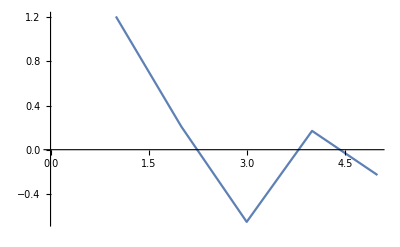

```mathematica
ListLinePlot[coefNoSARIMA[[1]]]
```

```mathematica
reducedDataset = unifyData[reducedOxyNo80,reducedOxyYes80];
partitioned=partitionTrainTest[reducedDataset,0.8];
```

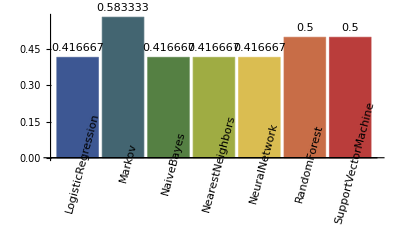

```mathematica
showPerformance[partitioned[[1]],partitioned[[2]] ]
```

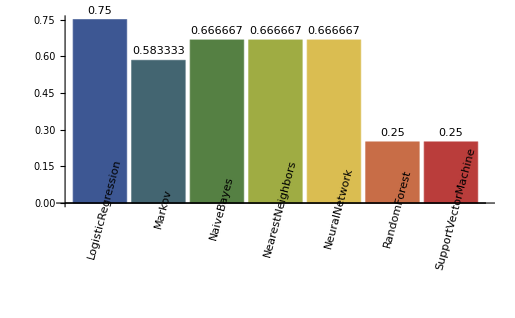

```mathematica
partitionFull = partitionTrainTest[fullDataYesAndNo,0.8];
showPerformance[partitionFull[[1]],partitionFull[[2]]]
```

```mathematica
logReg = Classify[partitionFull[[1]],Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
ClassifierMeasurements[logReg,partitionFull[[2]], "Accuracy"]
```

0.75

```mathematica
Options[logReg]
```

{<|Basic→<|ExampleNumber→48,FeatureNumber→15,ClassNumber→2|>,Input→<|Preprocessor→ToMLDataset,Processor→  ImputeMissing
ImputeMissing
ImputeMissing
ImputeMissing
ImputeMissing
ImputeMissing
ImputeMissing
ImputeMissing
ImputeMissing
ImputeMissing
ImputeMissing
ImputeMissing
ImputeMissing
ImputeMissing
ImputeMissing→Standardize
Standardize
Standardize
Standardize
Standardize
Standardize
Standardize
Standardize
Standardize
Standardize
Standardize
Standardize
Standardize
Standardize
Standardize|>,Output→<|Preprocessor→ToMLDataset,Processor→  ToVector→IntegerEncodeNominalVector→FromVector→FirstValues,ProbabilityPostprocessor→Identity,Name→class,Marginal→<|No→0.44,Yes→0.56|>|>,Combiner→First,Decision→<|Prior→Automatic,Utility→SparseArray[<4>, {2, 3}],Threshold→0,TieBreaker→RandomChoice,PerformanceGoal→Automatic,BatchProcessing→Automatic|>,Models→{<|Theta→{-0.00584951,-0.0464408,0.0153424,0.00867003,-0.00259984,0.0067342,0.000366015,-0.00807723,-0.000705371,0.00300492,0.00380549},L1Regularization→0,L2Regularization→1000.,FeatureNumber→10,Method→LogisticRegression,Processor→    NumericalSequenceToNumericalBag→NumericalBagStatistics
  NumericalSequenceToNumericalBag→NumericalBagStatistics
  NumericalSequenceToNumericalBag→NumericalBagStatistics
  NumericalSequenceToNumericalBag→NumericalBagStatistics
  NumericalSequenceToNumericalBag→NumericalBagStatistics
  NumericalSequenceToNumericalBag→NumericalBagStatistics
  NumericalSequenceToNumericalBag→NumericalBagStatistics
  NumericalSequenceToNumericalBag→NumericalBagStatistics
  NumericalSequenceToNumericalBag→NumericalBagStatistics
  NumericalSequenceToNumericalBag→NumericalBagStatistics
  NumericalSequenceToNumericalBag→NumericalBagStatistics
  NumericalSequenceToNumericalBag→NumericalBagStatistics
  NumericalSequenceToNumericalBag→NumericalBagStatistics
  NumericalSequenceToNumericalBag→NumericalBagStatistics
  NumericalSequenceToNumericalBag→NumericalBagStatistics→MergeVectors→DimensionReduceNumericalVector→PrependOne→FirstValues|>},Log→<|TrainingTime→0.682593,MaxTrainingMemory→1427080,DataMemory→502336,FunctionMemory→421592,LanguageVersion→{11.,0},Date→Mon 16 Apr 2018 13:41:31GMT+2.,ProcessorCount→2,ProcessorType→x86-64,OperatingSystem→MacOSX,SystemWordLength→64,Evaluations→{}|>|>}

```mathematica
unifyDataSARIMA[yes_List,no_List]:= Join[Thread[Table[yes[[x]],{x,Length[yes]}]-> "Yes"],Thread[Table[no[[x]],{x,Length[no]}]->"No"]]
reducedDatasetSARIMA = unifyDataSARIMA[coefYesSARIMA,coefNoSARIMA];
partitioned=partitionTrainTest[reducedDatasetSARIMA,0.7];
```

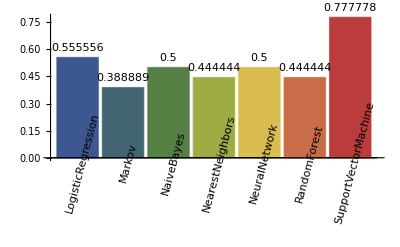

```mathematica
showPerformance[partitioned[[1]],partitioned[[2]] ]
```

```mathematica
wrpCustomArchYes[signal_List] :=Table[WarpingDistance[signal[[y]],archetypalMeanYes[[y]],DistanceFunction-> EuclideanDistance],{y,2}];
```

```mathematica
wrpCustomArchYes[signal_List] :=Table[WarpingDistance[signal[[y]],archetypalMeanYes[[y]]],{y,2}];
wrpCustomArchNo[signal_List] :=Table[WarpingDistance[signal[[y]],archetypalMeanNo[[y]]],{y,2}];
```

```mathematica
wrpFeat[signal_List]:= {wrpCustomArchYes[signal],wrpCustomArchNo[signal]}
```

```mathematica
wrpYes = Table[wrpFeat[reducedOxyYes80[[x]]],{x,30}];
```

```mathematica
wrpNo = Table[wrpFeat[reducedOxyNo80[[x]]],{x,30}];
```

```mathematica
unifyDataWrp[yes_List,no_List]:= Join[Thread[Table[yes[[x]],{x,Length[yes]}]-> "Yes"],Thread[Table[no[[x]],{x,Length[no]}]->"No"]]
```

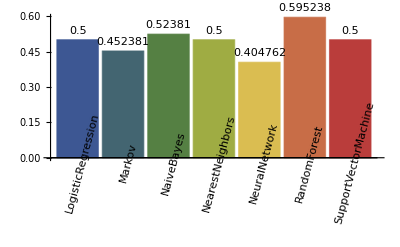

```mathematica
fullWrp = unifyDataWrp[wrpYes,wrpNo];
partWrp = partitionTrainTest[fullWrp,0.3];
showPerformance[partWrp[[1]],partWrp[[2]]]
```